# Knockout experiment

```mathematica
c=299.792458;(* mm/ns *)
mp=938.27203;
mn=939.56536;
mHe4=3728.401;
mB11=10255.1;
mC12=11178;
mN13=12114.77;
mN21=19586.63;
mO13=12132.54;
mO14=13048.92;
mO21=19569.44;
mO22=20502.15;
mO23=21438.98;
mO24=22374.93;
mF23=21427.69;
mF24=22363.42;
md=1875.612793;
massList={mp->"π",mn->"μ",mHe4->"α",mB11->"B11",mC12->"C12",mN13->"N13",mN21->"N21",mO13->"O13",mO14->"O14",mO21->"O21",mO22->"O22",mF23-> "F23"};
```

## Functions

```mathematica
(* all angel in radian, except for display *)
```

### Titled Lorentz Transfrom

The Lorentz Tranform on aribtary direction is well discrpted in Goldstien P .281

```mathematica
(* basis right-hand rotation operator *)
Rz[θ_]:={{1,0,0,0},{0,Cos[θ],Sin[θ],0},{0,-Sin[θ],Cos[θ],0},{0,0,0,1}};
Ry[θ_]:={{1,0,0,0},{0,Cos[θ],0,-Sin[θ]},{0,0,1,0},{0,Sin[θ],0,Cos[θ]}};
(* coordinate transform *)
Lz[β_]:={{1/(√(1-β^2)),0,0,β/(√(1-β^2))},{0,1,0,0},{0,0,1,0},{β/(√(1-β^2)),0,0,1/(√(1-β^2))}};
(* title Lorentz operator *)
L[β_,θ_,ϕ_]:= Rz[-ϕ].Ry[-θ].Lz[β].Ry[θ].Rz[ϕ]
```

### Rotation on (θ, ϕ) from Left Side

```mathematica
R[ϕNN_,θ_,ϕ_]:=Rz[-ϕ].Ry[-θ].Rz[ϕNN].Ry[θ].Rz[ϕ];
```

```mathematica
Manipulate[Graphics3D[{
{Gray,Line[{{0,0,0},{1,0,0}}]},
Text["x",{1,0,0}],
{Gray,Line[{{0,0,0},{0,1,0}}]},
Text["y",{0,1,0}],
{Gray,Line[{{0,0,0},{0,0,1}}]},
Text["z",{0,0,1}],
{Red,Arrow[{{0,0,0},{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}}]},
{Blue,Arrow[{{0,0,0},Drop[R[ϕNN,θ,ϕ].{0,Sin[θ+θNN]Cos[ϕ],Sin[θ+θNN]Sin[ϕ],Cos[θ+θNN]},{1}]}]}
},PlotRange->1,ViewPoint->{15,10,7}],{θ,0,π},{ϕ,0,2π},{θNN,0,π},{ϕNN,0,2π}]
```

### basic convertors

```mathematica
Mass[E_,k_]:=√(E^2-k^2);
Momentum[A_]:=Norm[A[[2;;4]]];
k2T[k_,m_]:=√(m^2+k^2)-m;
KE[A_,m_]:=A[[1]]-m
T2k[T_,m_]:=√(2m T+T^2);
(* θ(0,π), ϕ(-π,π) *)
Angle[A_]:=If[A[[2]]==0 && A[[3]]==0,{If[A[[4]]>0,0,π],0},{ArcTan[A[[4]],√(A[[2]]^2+A[[3]]^2)],ArcTan[A[[2]],A[[3]]]}];
ϕCorr[ϕ_]:=If[ϕ>0,π-ϕ,-ϕ-π]
(* angle between 2 vector*)
ΔAngle[A_,B_]:=ArcCos[(A[[2]]B[[2]]+A[[3]]B[[3]]+A[[4]]B[[4]])/(Momentum[A]Momentum[B])];
(* Display DisVector *)
DisVector[A_,name_]:={name,A[[1]],A[[2]],A[[3]],A[[4]]}
(* display (K.E. , momentum, angle 0 *)
β[A_]:=Momentum[A]/A[[1]]
DisEnergy[A_,m_,name_]:={name,A[[1]]-m,Momentum[A],Angle[A][[1]] ,Angle[A][[2]]}
```

```mathematica
(* 2 way to declare momentum 4-vector *)
PX[EX_,kX_,θX_,ϕX_]:={EX,kX Sin[θX]Cos[ϕX],kX Sin[θX]Sin[ϕX],kX Cos[θX]};
P[T_,m_,θ_,ϕ_]:={m+T,T2k[T,m]Sin[θ] Cos[ϕ],T2k[T,m] Sin[θ]Sin[ϕ],T2k[T,m] Cos[θ]};
```

### Detectors Geometry

```mathematica
FL[V_]:=(2 1400)/(√3 Abs[Cos[Angle[V][[2]]]]Sin[Angle[V][[1]]]+Cos[Angle[V][[1]]])
ToF[V_]:=FL[V]/(β[V]c)
Sp[V1_,V2_,T_]:=Module[{β,γ},
γ=(mp+T)/mp;
β=√(1-1/γ^2);
(1+γ)mp-γ(V1[[1]]+V2[[1]])+γ β(V1[[4]]+V2[[4]])]
Sp2[V1_,V2_,T_]:=√((PAXL[[1]]+PaXL[[1]]-P1XL[[1]]-P2XL[[1]])^2-Momt[PAXL-P1XL-P2XL]^2)-(mA-mb)
f[x_]:=Piecewise[{{3/2(x+170),200 2/3-170>x>-170},{200,200 (-2/3)+950>x>200 2/3-170},{-3/2(x-950),950>x>200 (-2/3)+950}},-1]
```

### Simulation

```mathematica
knockout[k_,θk_,ϕk_,θNN_,ϕNN_,S_,mInc_,mTar_,m_,TiL_]:={
PI=PX[mTar+TiL,√(2mTar TiL+TiL^2),π,0];
Pn=PX[mInc-√((mInc-m+S)^2+k^2),k,θk,ϕk]; (* fake 4 vector, for construct the CM frame of a-X*)
Pc=(PI+Pn)/2;
βPc=β[Pc];
{θPc,ϕPc}=Angle[Pc];
(* in CM frame of a X *)
Pcc=Pc.L[-βPc,θPc,ϕPc];
PIc=PI.L[-βPc,θPc,ϕPc];
Pnc=Pn.L[-βPc,θPc,ϕPc];
{θIc,ϕIc}=Angle[PIc];
Etotal=√(1-βPc^2)(PI[[1]]+Pn[[1]]); (* total energy of E1c and E2c *)
k1c=1/(2 Etotal)(√((Etotal-mTar-m)(Etotal+mTar-m) (Etotal-mTar+m) (Etotal+mTar+m)));
P1c={√(mTar^2+k1c^2),k1c Sin[θIc+θNN]Cos[ϕIc],k1c Sin[θIc+θNN]Sin[ϕIc], k1c Cos[θIc+θNN]}.R[ϕNN,θIc,ϕIc];
P2c={√(m^2+k1c^2) ,k1c Sin[θIc+θNN+π]Cos[ϕIc],k1c Sin[θIc+θNN+π]Sin[ϕIc], k1c Cos[θIc+θNN+π]}.R[ϕNN,θIc,ϕIc];
P1=P1c.L[βPc,θPc,ϕPc];
P2=P2c.L[βPc,θPc,ϕPc];
βPI=β[PI];
{θPI,ϕPI}=Angle[PI];
PIL=PI.L[-βPI,θPI,ϕPI];
PnL=Pn.L[-βPI,θPI,ϕPI];
P1L=P1.L[-βPI,θPI,ϕPI];
P2L=P2.L[-βPI,θPI,ϕPI];
SnOnline=mTar-1/(√(1-βPI^2)) m-(1/(√(1-βPI^2)) (P1L[[1]]-mTar+P2L[[1]]-m)- βPI/(√(1-βPI^2)) (Abs[P1L[[4]]+P2L[[4]]]));
Sn=√((PI[[1]]+mInc-P1[[1]]-P2[[1]])^2-Momentum[PI-P1-P2]^2)-(mInc-m);
(* output *)
P1L,P2L
}
```

## Simulation

```mathematica
Manipulate[knockout[k,θk °,ϕk °,θNN °,ϕNN °,S,mInc,m1,m2,TiL];
TableForm[
{{NumberForm[TableForm[Chop[{
"Setting",{"k",k,"θk, ϕk",θk  ,ϕk  },{"S",S,"θNN, ϕNN",θNN  ,ϕNN  },
{"βPI",βPI},
{"SnOnline", SnOnline},
{"Sn", Sn},
{"Lab frame", "----", "----", "----"},DisVector[PIL,"PIL"],DisVector[PnL,"PnL"],DisVector[P1L,"P1L"],DisVector[P2L,"P2L"],"",
{"", "K.E." , "Momentum", "θ" , "ϕ"},DisEnergy[P1L,m1,"P1L"] ,DisEnergy[P2L,m2,"P2L"],{"β1" , β[P1L],"β2" , β[P2L]},{"Δθ",(Angle[P1L][[1]]+Angle[P2L][[1]])180/π,"Δϕ",(Angle[P1L][[2]]-Angle[P2L][[2]])180/π},
{"Nucleus frame ", "----", "----", "----"},DisVector[PI,"PI"],DisVector[Pn,"Pn"],DisEnergy[Pn,m2,""],DisVector[P1,"P1"],DisVector[P2,"P2"],DisVector[P1+P2-PI-Pn,"Diff"],
{"Lorentz", "----", "----", "----"},DisVector[Pc,"Pc"],DisEnergy[Pc,0,""],{"β" , βPc,"γ", 1/(√(1-βPc^2))},DisVector[Pcc,"pcc"],
{"CM frame", "----", "----", "----"},DisVector[PIc,"PIc"],DisVector[Pnc,"Pnc"],DisVector[P1c,"k1c"],DisVector[P2c,"P2c"]
}],TableAlignments->{Right}],6],
Graphics[{
{Black,Arrow[{{PI[[2]],PI[[4]]},{0,0}}]},
{Blue,Arrow[{{0,0},{P1L[[2]],P1L[[4]]}}]},
{Red,Arrow[{{0,0},{P2L[[2]],P2L[[4]]}}]},
{Orange,Arrow[{-{PnL[[2]],PnL[[4]]},{0,0}}]}
},PlotRange->800,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotLabel-> "Lab, S="<>ToString[S]<>", k="<>ToString[k]<>", θ_k="<>ToString[θk ]<>"°, θ_NN="<>ToString[θNN ]<>"°, ΣT="<>ToString[DisEnergy[P2L,m2,""][[2]]+DisEnergy[P1L,m1,""][[2]]],Epilog->{Text["θ1L="<>ToString[180-Angle[P1L][[1]] 180/π]<>"\nβ1="<>ToString[β[P1L]]<>"\nT1="<>ToString[DisEnergy[P1L,m1,""][[2]]],{P1L[[2]],P1L[[4]]-90}],Text["θ2L="<>ToString[180-Angle[P2L][[1]] 180/π]<>"\nβ2="<>ToString[β[P2L]]<>"\nT2="<>ToString[DisEnergy[P2L,m2,""][[2]]],{P2L[[2]],P2L[[4]]-90}],
Text["Nucleus",{PI[[2]]+150,PI[[4]]-100}],
Text["Orbital Neutron",{-PnL[[2]]-200,-PnL[[4]]-50}],
Text["ΔAngle ="<>ToString[ΔAngle[P1L,P2L] 180/π],{500,-500}]},ImageSize->400],
{Graphics[{
{Purple,Arrow[{-{PI[[2]],PI[[4]]},{0,0}}]},
{Blue,Arrow[{{0,0},{P1[[2]],P1[[4]]}}]},
{Red,Arrow[{{0,0},{P2[[2]],P2[[4]]}}]},
{Green,Arrow[{{0,0},{Pc[[2]],Pc[[4]]}}]},
{Orange,Arrow[{-{Pn[[2]],Pn[[4]]},{0,0}}]}
},PlotRange->800,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotLabel-> "Nucleus",ImageSize->250]
,
Graphics[{
{Purple,Arrow[{-{PIc[[2]],PIc[[4]]},{0,0}}]},
{Blue,Arrow[{{0,0},{P1c[[2]],P1c[[4]]}}]},
{Red,Arrow[{{0,0},{P2c[[2]],P2c[[4]]}}]},
{Orange,Arrow[{-{Pnc[[2]],Pnc[[4]]},{0,0}}]}
},PlotRange->800,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotLabel-> "C.Momemtum",
Epilog->{Text["T_tot="<>ToString[DisEnergy[PIc,mp,""][[2]]+DisEnergy[Pnc,mn,""][[2]]],{0,500}]},ImageSize->250]
}
}
}]
,{{m1,mp},{mp->"Proton",mn->"Neutron"}},{{m2,mp},{mp->"Proton",mn->"Neutron",mHe4->"alpha"}},{{mInc,mO14},massList},{{TiL,250},0,280},{{k,100},0,100},{{θk,90},-180,180},{{ϕk,0},-180,180},{{S,30},0,30},{{θNN,90},-180,180},{{ϕNN,0},-180,360},ControlPlacement->Top]
```

## Monte Carlo

```mathematica
n=60000;
TKEA=245.402;
kM=Table[RandomReal[{0,200}],{i,1,n}];
SpM=Table[RandomChoice[4.627+{0,3.5,9.54,11.74}],{i,1,n}];
θkList=Table[ArcCos[2RandomReal[{0,1}]-1],{i,1,n}];
ϕkList=Table[ π RandomReal[{-1,1}],{i,1,n}];
θNNList=Table[ArcCos[2RandomReal[{0,1}]-1],{i,1,n}];
ϕNNList=Table[π RandomReal[{-1,1}],{i,1,n}];
(*DensityHistogram[
Table[{θkList[[i]],ϕkList[[i]]},{i,1,n}]
,{0.1}]*)
(* outputList = {P1L, P2L} *)
DataList=Monitor[Table[knockout[kM[[i]],θkList[[i]] ,ϕkList[[i]] ,θNNList[[i]] ,ϕNNList[[i]],SpM[[i]],mO14,mp,mp,TKEA],{i,1,n}],i];
(* Rearrange Data, π/2>Angle[V][[2]]>-π/2 should be the frist*)
ArrgDataList=Table[
If[ π/2≥ Angle[DataList[[i,1]]][[2]]≥ -π/2 ,DataList[[i]],{DataList[[i,2]],DataList[[i,1]]}]
,{i,1,n}];
```

```mathematica
Observable[list_]:=Monitor[Table[{
(*1 *) FL[list[[i,1]]],
(*2 *) FL[list[[i,2]]],
(*3 *) ToF[list[[i,1]]],
(*4 *) ToF[list[[i,2]]],
(*5 *) Angle[list[[i,1]]],
(*6 *) Angle[list[[i,2]]],
(*7 *) KE[list[[i,1]],mp],
(*8 *) KE[list[[i,2]],mp],
(*9 *) β[list[[i,1]]],
(*10 *) β[list[[i,2]]],
(* 11 *) Sp[list[[i,1]],list[[i,2]],TKEA],
(* 12 *) KE[list[[i,1]],mp]+KE[list[[i,2]],mp],
(* 13 *) Sp2[list[[i,1]],list[[i,2]],TKEA]
},{i,1,Length[list]}],i]
```

```mathematica
DataObser=Observable[ArrgDataList];
```

Part::partd: Part specification PAXL ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification PaXL ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification P1XL ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

$Aborted

```mathematica
Length[Select[DataObser,π/2>#[[6,2]]>-π/2&]]
```

273

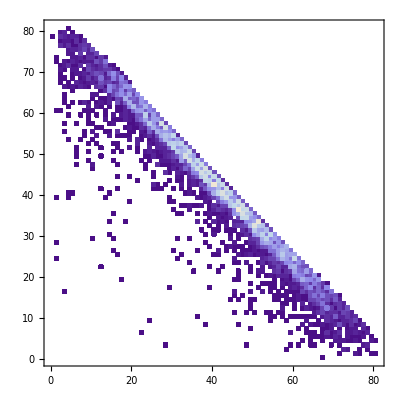

```mathematica
DensityHistogram[
Table[{DataObser[[i,5,1]],DataObser[[i,6,1]]}180/π,{i,1,n}],{{0, 90,1},{0,90,1}}
]
```

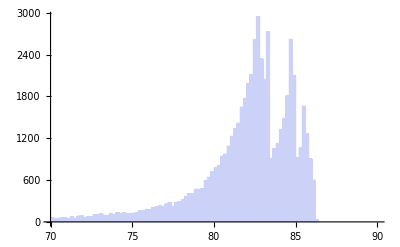

```mathematica
Histogram[
Table[(DataObser[[i,5,1]]+DataObser[[i,6,1]])180/π,{i,1,n}],{70,90,0.2}
]
```

```mathematica
DensityHistogram[
Table[{DataObser[[i,5,2]],ϕCorr[DataObser[[i,6,2]]]}180/π,{i,1,n}],{{-30,30,1},{-30,30,1}}
]
```

$Aborted[]

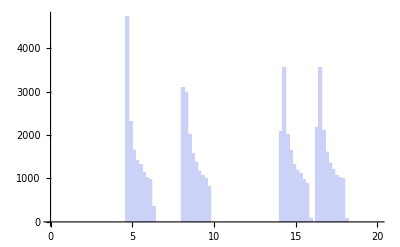

```mathematica
Histogram[
Table[DataObser[[i,11]],{i,1,n}],{0, 20, 0.2}
]
```

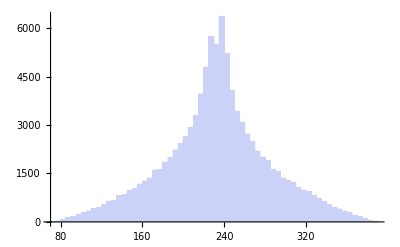

```mathematica
Histogram[
Table[DataObser[[i,12]],{i,1,n}]
]
```

## Detector Resolution

```mathematica
Rot1=RotationMatrix[60°,{0,-1,0}];
Rot2=RotationMatrix[60°,{0,1,0}];
```

```mathematica
(* the change of ToF but not angle *)
σTof=0.5;
MSToF1=Table[DataObser[[i,3]]+RandomVariate[NormalDistribution[0,σTof]],{i,1,n}];
MSToF2=Table[DataObser[[i,4]]+RandomVariate[NormalDistribution[0,σTof]],{i,1,n}];
MSXY1=Table[DataObser[[i,1]] 1022.37/1400 Normalize[ArrgDataList[[i,1]][[2;;4]]],{i,1,n}];
MSXY2=Table[DataObser[[i,2]] 1022.37/1400 Normalize[ArrgDataList[[i,2]][[2;;4]]],{i,1,n}];
MWDCcoord1=Table[Rot1.MSXY1[[i]],{i,1,n}];
MWDCcoord2=Table[Rot2.MSXY2[[i]],{i,1,n}];
(* Filter events by MWDC detection area , Filter will select MWDC pos and ToF*)
Filtered=Select[
Table[
If[
(f[-MWDCcoord1[[i,1]]]>Abs[MWDCcoord1[[i,2]]]) &&( f[MWDCcoord2[[i,1]]]>Abs[MWDCcoord2[[i,2]]]),
{MWDCcoord1[[i]],MWDCcoord2[[i]],MSToF1[[i]],MSToF2[[i]]},
{{0,0,0},{0,0,0}}
]
,{i,1,n}]
,#≠{{0,0,0},{0,0,0}}&];
m=Length[Filtered]
Pos1=Table[
Rot2.{
Filtered[[i,1,1]]+RandomVariate[NormalDistribution[0,0.2]],
Filtered[[i,1,2]]+RandomVariate[NormalDistribution[0,3]],
Filtered[[i,1,3]]},{i,1,m}];
Pos2=Table[
Rot1.{
Filtered[[i,2,1]]+RandomVariate[NormalDistribution[0,0.2]],
Filtered[[i,2,2]]+RandomVariate[NormalDistribution[0,3]],
Filtered[[i,2,3]]},{i,1,m}];
Graphics3D[{
Arrow[{{0,0,0},{0,0,1400}}],
Arrow[{{0,0,0},Rot1.{0,0,1400}}],
Arrow[{{0,0,0},Rot2.{0,0,1400}}],
Point[Pos1],
Point[Pos2]
(*Blue,PointSize[Small],Point[MSXY]*)
}]
FL1=Table[Norm[Pos1[[i]]] 1400/1022.37,{i,1,m}];
β1=Table[FL1[[i]]/(Filtered[[i,3]] c),{i,1,m}];
T1=Table[mp/(√(1-β1[[i]]^2))-mp,{i,1,m}];
FL2=Table[Norm[Pos2[[i]]] 1400/1022.37,{i,1,m}];
β2=Table[FL2[[i]]/(Filtered[[i,4]] c),{i,1,m}];
T2=Table[mp/(√(1-β2[[i]]^2))-mp,{i,1,m}];
```

548

-Graphics3D-

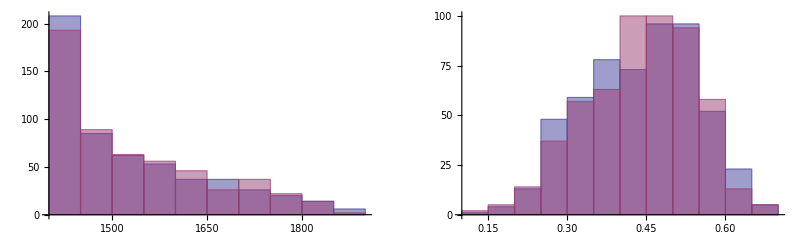

```mathematica
GraphicsGrid[{{Histogram[{FL1,FL2}],Histogram[{β1,β2}]}},ImageSize->800]
```

```mathematica
Measure=Table[
{Join[{T1[[i]]+mp},√(2 mp T1[[i]]+T1[[i]]^2)Normalize[Pos1[[i]]]],
Join[{T2[[i]]+mp},√(2 mp T2[[i]]+T2[[i]]^2)Normalize[Pos2[[i]]]]
},{i,1,m}];
MeasureObser=Observable[Measure];
```

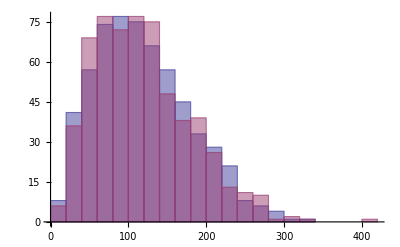

```mathematica
Histogram[
{
Table[MeasureObser[[i,7]],{i,1,m}],
Table[MeasureObser[[i,8]],{i,1,m}]
}]
```

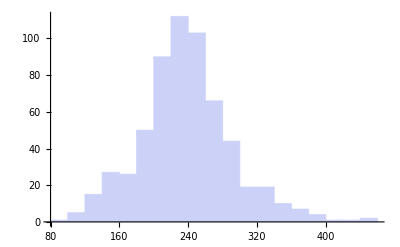

```mathematica
Histogram[
Table[MeasureObser[[i,12]],{i,1,m}]
]
```

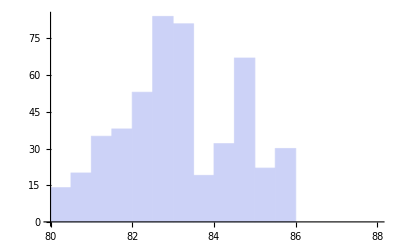

```mathematica
Histogram[
Table[(MeasureObser[[i,5,1]]+MeasureObser[[i,6,1]])180/π,{i,1,m}],{80,88,0.5}
]
```

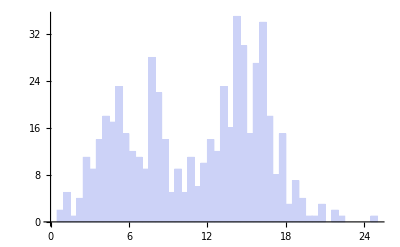

```mathematica
Histogram[
Table[MeasureObser[[i,11]],{i,1,m}],{0, 25,0.5}
]
```

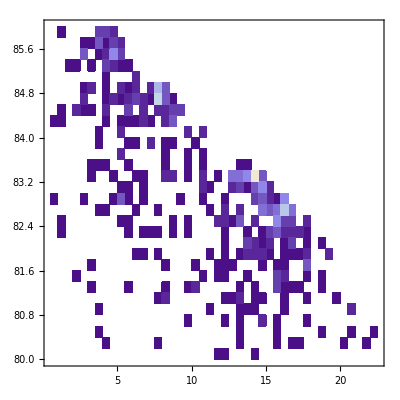

```mathematica
DensityHistogram[
Table[{MeasureObser[[i,11]],(MeasureObser[[i,5,1]]+MeasureObser[[i,6,1]])180/π},{i,1,m}],{{0,40,0.5},{80,100,0.2}}
]
```

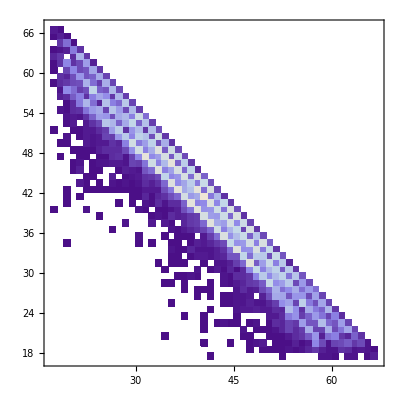

```mathematica
DensityHistogram[
Table[{MeasureObser[[i,5,1]],MeasureObser[[i,6,1]]}180/π,{i,1,m}],{{10,70,1},{10,70,1}}
]
```

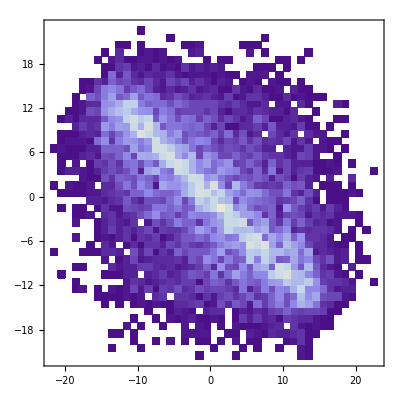

```mathematica
DensityHistogram[
Table[{MeasureObser[[i,5,2]],ϕCorr[MeasureObser[[i,6,2]]]}180/π,{i,1,m}],{{-30,30,1},{-30,30,1}}
]
```

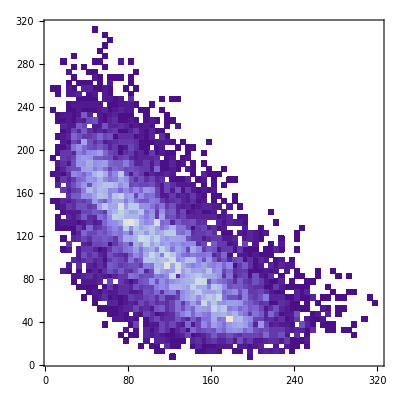

```mathematica
DensityHistogram[
Table[{MeasureObser[[i,7]],MeasureObser[[i,8]]},{i,1,m}],{{0,320,5},{0,320,5}}
]
```

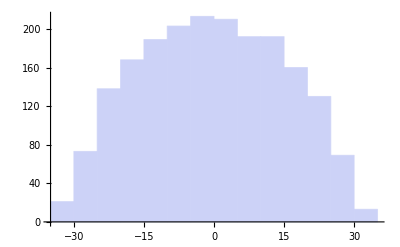

```mathematica
Histogram[
Table[(MeasureObser[[i,5,2]]-ϕCorr[MeasureObser[[i,6,2]]])180/π,{i,1,m}]
]
```